All the following functions are the same as that in CompleteGenericMatrices1D.nb. We will just be using different basis functions.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_moments_deal/Mathematica_files

```mathematica
colorlist={Black,Blue,Red,Darker[Green],Darker[Yellow],Orange,Lighter[Green],Lighter[Brown],Purple,Cyan}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

# Core routines

## Project individual tensors

The following function develos the projector for tensors of a particular degree

### From Manuel

```mathematica
ProjectTensor[degree_,nx_,ny_]:=Module[{result,n20,n02,n11,n30,n21,n12,n03,n40,n31,n22,n13,n04,n50,
n41,n32,n23,n14,n05,n60,n51,n42,n33,n24,n15,n06,n70,n61,n52,n43,n34,n25,n16,n07},

n20=nx*nx;n02=ny*ny;n11=nx*ny;

n30=nx*n20;n21=ny*n20;n12=ny*n11;n03=ny*n02;

n40=nx*n30;n31=ny*n30;n22=nx*n12;n13=nx*n03;n04=ny*n03;

n50=nx*n40;
n41=ny*n40;n32=nx*n22;n23=nx*n13;n14=ny*n13;n05=ny*n04;

n60=nx*n50;n51=ny*n50;n42=nx*n32;n33=nx*n23;n24=ny*n23;n15=ny*n14;n06=ny*n05;


n70=nx*n60;n61=ny*n60;n52=nx*n42;n43=nx*n33;n34=ny*n33;n25=ny*n24;n16=ny*n15;n07=ny*n06;


Which[degree == 0,
result = {1},
degree == 1,
result = {nx,ny,-ny,nx};
result=ArrayReshape[result,{2,2}];,
degree == 2,
result = {nx*nx,2*nx*ny,ny*ny,-nx*ny,nx*nx-ny*ny,nx*ny,ny*ny,-2*nx*ny,nx*nx};
result=ArrayReshape[result,{3,3}];,
degree == 3,
result = {nx*nx*nx,3*ny*nx*nx,3*nx*ny*ny,ny*ny*ny,-ny*nx*nx,nx*nx*nx-2*nx*ny*ny,2*ny*nx*nx-ny*ny*ny,nx*ny*ny,nx*ny*ny,-2*ny*nx*nx+ny*ny*ny,nx*nx*nx-2*nx*ny*ny,ny*nx*nx,-ny*ny*ny,3*nx*ny*ny,-3*ny*nx*nx,nx*nx*nx};
result=ArrayReshape[result,{4,4}];,
degree ==4,
result = {n40,4*n31,6*n22,4*n13,n04,-n31,-3*n22+n40,-3*n13+3*n31,-n04+3*n22,n13,n22,2*n13-2*n31,n04-4*n22+n40,-2*n13+2*n31,n22,-n13,-n04+3*n22,3*n13-3*n31,-3*n22+n40,n31,n04,-4*n13,6*n22,-4*n31,n40};

result = ArrayReshape[result,{degree+1,degree+1}];,
degree == 5,
result = {n50,5*n41,10*n32,10*n23,5*n14,n05,-n41,-4*n32+n50,-6*n23+4*n41,-4*n14+6*n32,-n05+4*n23,n14,n32,3*n23-2*n41,3*n14-6*n32+n50,n05-6*n23+3*n41,-2*n14+3*n32,n23,-n23,-2*n14+3*n32,-n05+6*n23-3*n41,3*n14-6*n32+n50,-3*n23+2*n41,n32,n14,n05-4*n23,-4*n14+6*n32,6*n23-4*n41,-4*n32+n50,n41,-n05,5*n14,-10*n23,10*n32,-5*n41,n50};

result=ArrayReshape[result,{degree+1,degree+1}];,
degree==6,
result = {n60,6*n51,15*n42,20*n33,15*n24,6*n15,n06,-n51,-5*n42+n60,-10*n33+5*n51,-10*n24+10*n42,-5*n15+10*n33,-n06+5*n24,n15,n42,4*n33-2*n51,6*n24-8*n42+n60,4*n15-12*n33+4*n51,n06-8*n24+6*n42,-2*n15+4*n33,n24,-n33,-3*n24+3*n42,-3*n15+9*n33-3*n51,-n06+9*n24-9*n42+n60,3*n15-9*n33+3*n51,-3*n24+3*n42,n33,n24,2*n15-4*n33,n06-8*n24+6*n42,-4*n15+12*n33-4*n51,6*n24-8*n42+n60,-4*n33+2*n51,n42,-n15,-n06+5*n24,5*n15-10*n33,-10*n24+10*n42,10*n33-5*n51,-5*n42+n60,n51,n06,-6*n15,15*n24,-20*n33,15*n42,-6*n51,n60};

result=ArrayReshape[result,{degree+1,degree+1}];,
degree == 7,
result = {n70,7*n61,21*n52,35*n43,35*n34,21*n25,7*n16,n07,-n61,-6*n52+n70,-15*n43+6*n61,-20*n34+15*n52,-15*n25+20*n43,-6*n16+15*n34,-n07+6*n25,n16,n52,5*n43-2*n61,10*n34-10*n52+n70,10*n25-20*n43+5*n61,5*n16-20*n34+10*n52,n07-10*n25+10*n43,-2*n16+5*n34,n25,-n43,-4*n34+3*n52,-6*n25+12*n43-3*n61,-4*n16+18*n34-12*n52+n70,-n07+12*n25-18*n43+4*n61,3*n16-12*n34+6*n52,-3*n25+4*n43,n34,n34,3*n25-4*n43,3*n16-12*n34+6*n52,n07-12*n25+18*n43-4*n61,-4*n16+18*n34-12*n52+n70,6*n25-12*n43+3*n61,-4*n34+3*n52,n43,-n25,-2*n16+5*n34,-n07+10*n25-10*n43,5*n16-20*n34+10*n52,-10*n25+20*n43-5*n61,10*n34-10*n52+n70,-5*n43+2*n61,n52,n16,n07-6*n25,-6*n16+15*n34,15*n25-20*n43,-20*n34+15*n52,15*n43-6*n61,-6*n52+n70,n61,-n07,7*n16,-21*n25,35*n34,-35*n43,21*n52,-7*n61,n70};

result=ArrayReshape[result,{degree+1,degree+1}];
];


result
]
```

### General Routine

```mathematica
ProjectorGeneral2D[deg_]:=Module[{result,project1,I,size,normalizer},
(*Projector for the first order tensor*)
project1 = {{nx,ny},{-ny,nx}};
result = 0;

If[deg==0,result = 1,result = project1;
Do[
size = Length[result];
result=KroneckerProduct[project1,result];

(*now we contract the result*)
I = ConstantArray[0,{Length[result],ii+1}];
I⟦1;;size,1;;size⟧=IdentityMatrix[size];
I⟦(size+1);;-1,-size;;-1⟧=IdentityMatrix[size];

result = Transpose[I].result.I;

 ,{ii,2,deg}];

(*extract the first coloumn of result*)
normalizer=Abs[result⟦All,1⟧/.{nx->1,ny->1}];

result =Simplify[Inverse[DiagonalMatrix[normalizer]].result];

];



result

]
```

### Check

```mathematica
Simplify[ProjectTensor[2,nx,ny]-ProjectorGeneral2D[2]]

Simplify[ProjectTensor[3,nx,ny]-ProjectorGeneral2D[3]]

Simplify[ProjectTensor[4,nx,ny]-ProjectorGeneral2D[4]]

Simplify[ProjectTensor[5,nx,ny]-ProjectorGeneral2D[5]]

Simplify[ProjectTensor[6,nx,ny]-ProjectorGeneral2D[6]]

Simplify[ProjectTensor[7,nx,ny]-ProjectorGeneral2D[7]]
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be 1. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsity2[a_,filename_,flag_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros},

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;-2]];

nnz = Length[indicies];
rowindicies = ConstantArray[0,Length[indicies]];
colindicies = ConstantArray[0,Length[indicies]];
entries = ConstantArray[0,Length[indicies]];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]]-1,{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]]-1,{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["../system_matrices/",filename]];

WriteString[str,ToString[nnz],"\n"];

Which[flag == 0,
Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[0],"\n"],{ii,1,Length[rowindicies]}];,
flag == 1,
Do[WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];
]

Close[str];

]

(*write a vector to a file*)
writeVector[vec_,filename_]:=Module[{NumEntries,str,destination},

NumEntries = Length[vec];

destination = StringJoin["../system_matrices/",filename];

(*first open the file to write*)
str = OpenWrite[destination];

(*first write the number of entries to the file*)
WriteString[str,ToString[NumEntries],"\n"];

(*write the vector to the opened file*)
Do[WriteString[str,ToString[vec[[ii]]],"\n"],{ii,1,Length[vec]}];

Close[str];

]
```

## Tensor Definitions

```mathematica
(*Remove["Global`*"]*)
```

Mathematica build-in function like ‘Symmetrize[]’ and ‘TensorContract[]’ seem 
to work really slow or fail due to memory requirements on fully symmetric tensors 
with degree >10.
We define our own functions below based on a simply array data structure for fully symmetric tensors.

```mathematica
Clear[n,degree,idx,idx1,A,b,id3,IDX]
Unprotect[TensorDegree];

(*Every symmetric tensor can be identified with the help of a 2D array say a[N][3] where N is the total number of indepedent variables it has. So every row ie a[i] store the number of entries for x in a[i][1],for y in a[i][2] and for z in a[i][3]*)
IDXFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,ii}],{ii,0,n}],1]

(*does the same thing as IDXFull but for trace free tensors*)
IDXtrfFull[n_]:=Flatten[Table[Table[{n-ii,ii-jj,jj},{jj,0,Min[ii,1]}],{ii,0,n}],1]

Do[
IDX[degree]=IDXFull[degree];
IDXtrf[degree]=IDXtrfFull[degree];
,{degree,0,40}]

(*given an array list, the following function counts the number of 1s, 2s and 3s*)
toIDX1[list_]:=Map[Count[list,#]&,{1,2,3}] (* Input cartesean indices, e.g. {1,1,2,1,3} *)

(*the Total of the list is the tensorial degree we are interested in. So list should be a 3X1 array and the following function will give us the n corresponding to which a[n] = list.*)
toIDX2[list_]:=Position[IDX[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)
(*same as above but for trace free tensors*)
toIDX3[list_]:=Position[IDXtrfFull[Total[list]],list]⟦1,1⟧ (* Input triple of #indices in {1,2,3} *)

(*Gives the tensor degree of a symmetric tensor.
CAUTION: the formulae is not valid for trace free tensors.*)
TensorDegree[A_]:=1/2 (-3+√(1+8 Length[A]))

id3={{1,0,0},{0,1,0},{0,0,1}};

DeltaValues[list_]:=Block[{a=list⟦1⟧,b=list⟦2⟧,c=list⟦3⟧},
If[OddQ[a]||OddQ[b]||OddQ[c],0,Multinomial[a/2,b/2,c/2]/Multinomial[a,b,c]]
];

(*applied deltavalues to all the components of an even degree tensor*)
DeltaTensor2[degree_?EvenQ]:=Map[DeltaValues,IDX[degree]];

(*What does this do?*)
SymTrace2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-2]⟦jj⟧+2 id3⟦ii⟧]⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

SymTraces[A_,n_]:=Module[{res=A},
Do[res=SymTrace2[res],{ii,1,n}];
res
];

(*if the format of the input is IDX, then the output is also in IDX,
Assumes 3 dimensions. And so *)
(* contraction of a symmetric tensor A with Subscript[b, i] *)
SymDot2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree-1]];
res=ConstantArray[0,length];
Do[
(*Lets take a particular term say Ai1i2..xbx. In the result only those components will appear in which x atleast appears once and that's why the addition of id3[[iis]]*)
res⟦jj⟧=Expand[Sum[A⟦toIDX2[IDX[degree-1]⟦jj⟧+id3⟦ii⟧]⟧b⟦ii⟧,{ii,1,dim}]];
,{jj,1,length}];

res
];

(*if the format of the input is IDX, then the output is also in IDX*)
(* full contraction of two symmetric tensors A, B with same degree *)
SymFullDot[A_,B_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[TensorDegree[B]≠degree,Return[0]];
length=Length[IDX[degree]];
res=0;
Do[
idx=IDX[degree]⟦jj⟧;
res+=Multinomial[idx⟦1⟧,idx⟦2⟧,idx⟦3⟧]A⟦jj⟧B⟦jj⟧;
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[b, i] *)
SymProduct2[A_,b_?VectorQ]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
If[degree==0,Return[A⟦1⟧ b]];
length=Length[IDX[degree+1]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=
1/(degree+1)Sum[
If[(idx=IDX[degree+1]⟦jj⟧)⟦ii⟧>0,idx⟦ii⟧ A⟦toIDX2[idx-id3⟦ii⟧]⟧b⟦ii⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(* symmetric tensor product of a symmetric tensor A with Subscript[δ, ij] *)
SymProductDelta2[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res},
length=Length[IDX[degree+2]];
res=ConstantArray[0,length];
Do[
res⟦jj⟧=1/((degree+2)(degree+1))Sum[
If[(idx=IDX[degree+2]⟦jj⟧)⟦ii⟧≥2,idx⟦ii⟧(idx⟦ii⟧-1)A⟦toIDX2[idx-2id3⟦ii⟧]⟧,0],{ii,1,dim}];
,{jj,1,length}];

res
];

(*converts a symmetric tensor into a trace free tensor*)
(* returns the tracefree part of a symmetric tensor, but with all components *)
SymTracefree[A_]:=Block[{dim=3,idx,idx1,degree=TensorDegree[A],length,res,trace,res1},
length=Length[IDX[degree]];
res=trace=A;
Do[
res1=trace=SymTrace2[trace];
Do[res1=SymProductDelta2[res1],{ll,1,kk}];
res+=(((-1)^kk degree!)/((degree-2kk)!2^kk kk!)∏_(jj=degree-kk)^(degree-1) 1/(2jj+1))res1;
,{kk,1,degree/2}];

res
];
```

```mathematica
trfEvaluate[A_,list_]:=Module[{a,b,c,m,dim=3,degree=(Length[A]-1)/2,length,res},
{a,b,c}=list;
m=Floor[c/2];
If[c≤1,
res=A⟦toIDX3[list]⟧,
res=(-1)^m Sum[Binomial[m,i]A⟦toIDX3[list+2i id3⟦1⟧+2(m-i) id3⟦2⟧-2m id3⟦3⟧]⟧,{i,0,m}]
];
res
];

(*say we have a trace free tensor, whose independent components are given then the following function will introduce those components in the list which have been negelected due to the trace free nature of the tensor. For eg. it will introduce -Rxx-Ryy for a second order tensor*)
trf2sym[A_]:=Map[Apply[trfEvaluate[A,{#1,#2,#3}]&,#]&,IDX[(Length[A]-1)/2]]

(*Pick the 2D variables from a list containing all the indices.The list will be obtained from the IDXtrf routine. freeindex is the total number of free indices in the tensor*)
Pick2D[freeindex_]:=Pick[IDXtrf[freeindex],Flatten[Join[{1},Table[{1,0},{k,1,freeindex}]]],1];
```

```mathematica
SymTensorForm[A_]:=Block[{degree=TensorDegree[A],length},
length=Length[IDX[degree]];
Table[Apply[{$[#1,#2,#3],A⟦ii⟧}&,IDX[degree]⟦ii⟧],{ii,1,length}]//TableForm
];
```

```mathematica
SymProductDelta2[SymProductDelta2[SymProductDelta2[Map[Apply[A[#1,#2,#3]&,#]&,IDX[1]]]]]
```

{A[1,0,0],1/7 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/7 A[1,0,0],3/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],3/35 A[0,0,1],3/35 A[1,0,0],0,1/35 A[1,0,0],0,3/35 A[1,0,0],1/7 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/35 A[0,0,1],1/35 A[0,1,0],1/7 A[0,0,1],1/7 A[1,0,0],0,1/35 A[1,0,0],0,1/35 A[1,0,0],0,1/7 A[1,0,0],A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],3/35 A[0,0,1],3/35 A[0,1,0],1/7 A[0,0,1],1/7 A[0,1,0],A[0,0,1]}

```mathematica
Expand[SymTracefree[Map[Apply[A[#1,#2,#3]&,#]&,IDX[2]]]]
```

{-1/3 A[0,0,2]-1/3 A[0,2,0]+2/3 A[2,0,0],A[1,1,0],A[1,0,1],-1/3 A[0,0,2]+2/3 A[0,2,0]-1/3 A[2,0,0],A[0,1,1],2/3 A[0,0,2]-1/3 A[0,2,0]-1/3 A[2,0,0]}

```mathematica
Expand[SymTracefree[Map[Apply[#1+2.#2-3#3&,#]&,IDX[4]]]]
```

{-1.14286,1.14286,2.57143,3.42857,1.42857,-2.28571,3.14286,2.85714,-4.28571,-5.42857,-2.28571,4.28571,-1.14286,-5.71429,3.42857}

```mathematica
Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]]
```

2 Rxx Sxx+Ryy Sxx+2 Rxy Sxy+Rxx Syy+2 Ryy Syy

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{Rxx,Rxy,0,Ryy,0}]],SymTracefree[trf2sym[{Sxx,Sxy,0,Syy,0}]]]],{Rxx,Rxy,Ryy}]]⟦2⟧,{Sxx,Sxy,Syy}]⟦2⟧]
```

{{2,0,1},{0,2,0},{1,0,2}}

```mathematica
Normal[CoefficientArrays[Normal[CoefficientArrays[Expand[SymFullDot[SymTracefree[trf2sym[{mxxx,mxxy,0,mxyy,0,myyy,0}]],SymTracefree[trf2sym[{nxxx,nxxy,0,nxyy,0,nyyy,0}]]]],{mxxx,mxxy,mxyy,myyy}]]⟦2⟧,{nxxx,nxxy,nxyy,nyyy}]⟦2⟧]
```

{{4,0,3,0},{0,6,0,3},{3,0,6,0},{0,3,0,4}}

## Basic Definitions

```mathematica
(*ref to manuels paper on fluxes for large moment system for a detailed expression*)
(*total tensorial degree including traces*)
iFullDegree[i_]=Floor[√(4i-3)-1];
(*number of traces C^2 has one trace*)
iTraces[i_]=Floor[(1+1/2 iFullDegree[i])^2]-i;
(*actual tensorial degree*)
iTensorDegree[i_]=iFullDegree[i]-2iTraces[i];
ii[s_,A_]=Floor[(A+2(s+1))/2](A+2(s+1)-Floor[(A+2(s+1))/2])-s;

(*i is as defined in the reference*)
NumberOfVariables2D[ntensors_]:=Sum[iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfVariables3D[ntensors_]:=Sum[2iTensorDegree[i]+1,{i,1,ntensors}];
NumberOfFullTensors3D[ntensors_]:=Block[{m=iFullDegree[ntensors],frac},
m-(((m+1)(m+2)(m+3))/6.-Sum[2iTensorDegree[i]+1,{i,1,ntensors}])/(((m+1)(m+2))/2)
];

varName[s_,ix_,iy_,iz_]:=StringJoin["ρ",ToString[s],ConstantArray["x",ix],ConstantArray["y",iy],ConstantArray["z",iz]]


(*this is not the norm of ψ, rather it's the norm of the laguerre polynomials*)
Normψ[a_,deg_]=(deg!a!Gamma[deg+a+3/2])/Gamma[deg+3/2];

(*given a tensor W extract all the independed components in 2D in case of trace free situation*)
trfComponents2D[W_]:=Extract[W,Map[Position[IDX[TensorDegree[W]],#]⟦1⟧&,Pick[IDXtrf[TensorDegree[W]],Flatten[Join[{1},Table[{1,0},{k,1,TensorDegree[W]}]]],1]]]


trfVar2D[deg_,name_]:=Table[name[i],{i,1,deg+1}]
From2Dto3D[list_]:=Flatten[Join[{list⟦1⟧},Table[{list⟦k⟧,0},{k,2,Length[list]}]]]


R2[0,1]={{1},{0}};
R2[0,2]={{0},{1}};

Do[
(*Given the components of a tensor represented by B, then tmp collects the terms corresponding to \partial_x in \partial_<x_{in} w_{i1..in>}
the second one does the same job but for a tensor product. *)
tmp=Normal[CoefficientArrays[trfComponents2D[SymDot2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]],{dx,dy}]]⟦2⟧;
(*store the coefficient infront of the moments*)
Do[R1[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];

(*same as above but for tensor products*)
tmp=Normal[CoefficientArrays[trfComponents2D[SymTracefree[SymProduct2[trf2sym[From2Dto3D[trfVar2D[d,B]]],{dx,dy,0}]]],{dx,dy}]]⟦2⟧;
(*store the coefficients infront of the moments*)
Do[R2[d,i]=CoefficientArrays[tmp⟦All,i⟧,trfVar2D[d,B]]⟦2⟧,{i,1,2}];
,{d,1,15}];

(*The following is the main moment equation*)
recursion1[a_,deg_,flag_]:=(
√((2 deg+2)/(2deg+3))(√(deg+a+3/2)R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a,deg+1]&]-√a R1[deg+1,flag].trfVar2D[deg+1,ψ[#,a-1,deg+1]&])
+If[deg>0,√((2deg)/(2deg+1))(√(deg+a+1/2)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a,deg-1]&]-√(a+1)R2[deg-1,flag].trfVar2D[deg-1,ψ[#,a+1,deg-1]&]),0])

(*(Give two Laguerre polynomials Subscript[(L^(n)), a] and Subscript[(L^(m)), b] then the following routine computes (∫^∞)_0 Subscript[(L^(n)(x^2/2)), a](L^(m)(x^2/2))))_b x^2 ⅇ^(-x^2/2)dx. Uses the Laguerre polynomials used in file CompleteGenericMatrices1D.nb*)
mixed[a_,n_,b_,m_]:=Expand[Sum[Binomial[n-(n+m)/2+a-c1-1,a-c1](a!)/(c1!)Binomial[m-(n+m)/2+b-c1-1,b-c1](b!)/(c1!)(c1!√2 Gamma[(n+m)/2+c1+3/2] 2^((n+m)/2)),{c1,0,Min[a,b]}]];

(*ratio between the new and old laguerre polynomials*)
factorLaguerre[a_,n_]:=√(Gamma[n+3/2]/(n!a!Gamma[n+a+3/2]));

(*Same as above but for Laguerre polynomials used in the Boundary Value problem paper*)
mixed2[a_,n_,b_,m_]:=Expand[mixed[a,n,b,m]factorLaguerre[a,n]factorLaguerre[b,m]];

(*The following function integrates expressions of the kind ∫νx^m νy^p νz^n dν but the integration is such that only νx >0. Making the transformation to spherical coordinates i.e. νx = Sin ν Cos θ, νy = Sin ν Sin θ and νz = Cos ν we have (∫^(+π/2))_(-π/2)(∫_0)^π(Sinν^(mm+nn+1)Cosν^pp Sinθ^nn Cosθ^mm)dνdθ*)

IntegrateHalfNxNyNz1[ex_]:=Block[{pos1,pos2,pos3,mm=0,nn=0,pp=0,res,res1=νx νy νz ex},
pos1=Position[res1,νx^_];
pos2=Position[res1,νy^_];
pos3=Position[res1,νz^_];
If[Length[pos1]>0,mm=Extract[res1,pos1⟦1⟧]⟦2⟧-1];
If[Length[pos2]>0,nn=Extract[res1,pos2⟦1⟧]⟦2⟧-1];
If[Length[pos3]>0,pp=Extract[res1,pos3⟦1⟧]⟦2⟧-1];
res=Delete[res1,Join[pos1,pos2,pos3]]If[OddQ[nn]||OddQ[pp],0,2π((nn-1)!!(mm-1)!!(pp-1)!!)/((nn+mm+pp+1)!!)];
If[Length[pos1]==0,res=res/νx];
If[Length[pos2]==0,res=res/νy];
If[Length[pos3]==0,res=res/νz];
res
]

(*applies integrate halfnxnynz1 to a long expression*)
IntegrateHalfNxNyNz[ex_]:=If[Head[ex]=== Plus,
Apply[Plus,Table[IntegrateHalfNxNyNz1[ex⟦ii⟧],{ii,1,Length[ex]}]],
IntegrateHalfNxNyNz1[ex]]


(*The input of the following function i.e idx1 and idx2 are arrays such that idx1[[{2,3,4}]] = {#xcomponents,#ycomponents,#zcomponents}. The following function computes the half integrals of the form ∫ ψ fdc where ψ is the basis function and the integral is only over the half space. The ψ is represented by one of the input parameters and the basis functions in f are represented by one of the input parameters.

idx1 = index for the testfunction
	   ix2 = index for the basis of the distribution function*)

HalfIntegrate[idx1_,idx2_]:=Block[{Int1,Int2,deg1=Total[idx1⟦{2,3,4}⟧],deg2=Total[idx2⟦{2,3,4}⟧],f0},

(*The following term develops terms of the form ν_(<x^m y^n>). The algorithm is as follows
1. Extract the total number of free indices in the tensor
2. Develop the full sym trace free tensor i.e develop all the components of ν_(<i_(1...)Subscript[i, n]>)
3. Extract the component corresponding to idx1*)

Int1=Expand[SymTracefree[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg1]]]⟦toIDX2[idx1⟦{2,3,4}⟧]⟧];

(*Let us consider the part of the distribution function which comes from Rij. This part will be of the form Rxx...+Rzz.... But Rzz = -Rxx-Ryy and therefore Int2 is not simply the tensorised ν_(<x^m y^n>)*)
Int2=SymFullDot[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg2]],trf2sym[Map[Apply[If[{#1,#2,#3}==idx2⟦{2,3,4}⟧,1,0]&,#]&,IDXtrf[deg2]]]];
f0= 1/(2 π)^(3/2);

Expand[mixed2[idx1⟦1⟧,deg1,idx2⟦1⟧,deg2]f0 IntegrateHalfNxNyNz[Expand[Int1 Int2]]]
]
```

## Mapping to Conventional Variables

```mathematica
MappingToConventional[Ntensors_]:=Module[{varIdx,varIdxComplete,conVar,resultGas,Var,resultWall},

(*compute the tensor degree and the number of traces for every tensor in the system.
In all the coming computations, iTraces will be represented by a.sa*)
varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];

(*same as IDXtrf but instead stores the value of the number of traces in the first argument of every list*)
varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,Pick[IDXtrf[varIdx⟦n,2⟧],Flatten[Join[{1},Table[{1,0},{k,1,varIdx⟦n,2⟧}]]],1]],{n,1,Length[varIdx]}],1];

(*Conventional Variables for comparison*)
conVar = {ρ,vx,vy,-√(3/2) θ,σxx/(√2),σxy/(√2),σyy/(√2),-√(2/5)qx,-√(2/5)qy,mxxx/(√6),mxxy/(√6),mxyy/(√6),myyy/(√6),Δ/(2 √30),-Rxx/(2 √7),-Rxy/(2 √7),-Ryy/(2 √7),φxxxx/(2 √6),φxxxy/(2 √6),φxxyy/(2 √6),φxyyy/(2 √6),φyyyy/(2 √6),Ωx/(2 √70),Ωy/(2 √70),-ψxxx/(6 √3),-ψxxy/(6 √3),-ψxyy/(6 √3),-ψyyy/(6 √3)};

Var = Map[Apply[w,#]&,varIdxComplete];

resultGas=Table[Var[[ii]]->conVar[[ii]],{ii,1,Length[Var]}];

resultWall = {Subscript[w, wall][0,0,0,0]->ρW,Subscript[w, wall][1,0,0,0]->-√(3/2) θW};

Flatten[{resultGas,resultWall}]
]

conversionMatrixG26 = DiagonalMatrix[{1,1,1,-√(3/2) ,1/(√2),1/(√2),1/(√2),-√(2/5),-√(2/5),1/(√6),1/(√6),1/(√6),1/(√6),1/(2 √30),-1/(2 √7),-1/(2 √7),-1/(2 √7)}];


conversionMatrixG45 = DiagonalMatrix[{1,1,1,-√(3/2),1/(√2),1/(√2),1/(√2),-√(2/5),-√(2/5),1/(√6),1/(√6),1/(√6),1/(√6),1/(2 √30),-1/(2 √7),-1/(2 √7),-1/(2 √7),1/(2 √6),1/(2 √6),1/(2 √6),1/(2 √6),1/(2 √6),1/(2 √70),1/(2 √70),-1/(6 √3),-1/(6 √3),-1/(6 √3),-1/(6 √3)}];

varConventional26 = {ρ,vx,vy,θ,σxx,σxy,σyy,qx,qy,mxxx,mxxy,mxyy,myyy,Δ,Rxx,Rxy,Ryy};

varConventional45 = {ρ,vx,vy,θ,σxx,σxy,σyy,qx,qy,mxxx,mxxy,mxyy,myyy,Δ,Rxx,Rxy,Ryy,φxxxx,φxxxy,φxxyy,φxyyy,φyyyy,Ωx,Ωy,ψxxx,ψxxy,ψxyy,ψyyy};
```

## Matrices generation

### System Matrices

```mathematica
GetMatrices2D[Ntensors_]:=Block[{varIdx,varIdxComplete,theory,normMatrix,varNames,var,Ax,Ay,
var1D,BCvar,varOdd,varIdxCompleteEven,varEven,BCraw,ρindex=1,vindex=2,ρWeqn,BCnum,BCrhs,Praw,BCraw2,varIdxCompleteOdd,IntGasEven,IntGasOdd,varIdxWall,IntWall,B,eqnVelocity},

(*compute the tensor degree and the number of traces for every tensor in the system.
In all the coming computations, iTraces will be represented by a.sa*)
varIdx=Table[{iTraces[i],iTensorDegree[i]},{i,1,Ntensors}];

(*same as IDXtrf but instead stores the value of the number of traces in the first argument of every list*)
varIdxComplete=Flatten[Table[Map[Join[{varIdx⟦n,1⟧},#]&,Pick[IDXtrf[varIdx⟦n,2⟧],Flatten[Join[{1},Table[{1,0},{k,1,varIdx⟦n,2⟧}]]],1]],{n,1,Length[varIdx]}],1];

(*variables for the wall. Density and Temperature*)
varIdxWall = {{0,0,0,0},{1,0,0,0}};

(*computes the number of traces for a given iTensorDegree. The final result gives us the tuple discussed in the paper on the convergence of the boundary value problem.*)
theory=Table[Count[varIdx,{_,k}],{k,0,iFullDegree[Ntensors]}];
(*Print["number of different tensor degrees: ",theory];
Print["corresponding variables (traces,indices): ",Flatten[Table[Table[{a,n-1},{a,0,theory⟦n⟧-1}],{n,1,Length[theory]}],1]];
Print["Number of Variables 1D: ",Ntensors];
Print["Number of Variables 2D: ",NumberOfVariables2D[Ntensors]];
Print["Number of Variables 3D: ",NumberOfVariables3D[Ntensors]];
Print["Number of full Tensors 3D: ",NumberOfFullTensors3D[Ntensors]];*)

normMatrix=DiagonalMatrix[SparseArray[Flatten[Map[Function[{a,deg},ConstantArray[Normψ[a,deg],deg+1]]@@#&,varIdx]]]];

(*So the stress tensor will be different from the usual stress tensor defined normally.
All the variable names are for the 2D case. *)
varNames=ToExpression[Map[varName@@#&,varIdxComplete]/.{"ρ0"->"ρ","ρ0x"->"vx","ρ0y"->"vy","ρ1"->"θ","ρ0xx"->"σxx","ρ0xy"->"σxy","ρ0yy"->"σyy","ρ1x"->"qx","ρ1y"->"qy"}]/.{θ->-3/2θ,qx->-qx,qy->-qy};


(*the result from var consists of the form ψ[n,a,deg], where a = #traces, deg = #free tensors and n is the name for eg vx = 1 and vy = 2 or θ is simply 1*)
var=Table[Apply[Function[{a,deg},trfVar2D[deg,ψ[#,a,deg]&]],item],{item,varIdx}];

Ax=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,1]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;
Ay=CoefficientArrays[Flatten[Table[Apply[Function[{a,deg},recursion1[a,deg,2]],item],{item,varIdx}]],Flatten[var]]⟦2⟧;

(*
(*reduction for 1d*)
var1D=Flatten[Position[Map[If[(#⟦3⟧==0)&&(#⟦4⟧==0),1,0]&,varIdxComplete],1]];
varIdxComplete=varIdxComplete⟦var1D⟧;
varNames=varNames⟦var1D⟧;
Ax=Normal[Ax⟦var1D,var1D⟧];
normMatrix=normMatrix⟦var1D,var1D⟧;
*)

(*As the literature says the boundary conditions will only be computed with basis functions which have odd powers of Cx(considering the normal to point in the x direction). BCVar is a mapping which collects odd basis functions *)
BCvar=Map[If[OddQ[#⟦2⟧],1,0]&,varIdxComplete];

(*the position of odd variables.*)
varOdd=Flatten[Position[BCvar,1]];

(*Picks out the even components. The fourth component is anyhow always zero.*)
varIdxCompleteEven=Select[varIdxComplete,(EvenQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Picks out the odd variables*)
varIdxCompleteOdd=Select[varIdxComplete,(OddQ[#⟦2⟧]&&#⟦4⟧==0)&];

(*Every element is same as that to varIdxCompleteEven. The following manupilation just separates out the elements depending upon the number of y-indices*)
Do[
varEven[jj,0]=Select[varIdxCompleteEven,(#⟦3⟧==jj)&],
{jj,0,Max[varIdxCompleteEven⟦All,3⟧]}];

(*In the following function we compute ∫ ψ f^even dc where ψ is such that the powers of Cx appearing in ψ are odd. The first argument of jj has been optimised using some currently unkown formula. The result from this manipulation remains the same even if {jj,idx[[3]],0,-2} is substituted by {jj,0,Max[varIdxCompleteEven⟦All,3⟧]}.
Let the basis function of f be ϕ and the test function be ψ. m = powers of Cy in ψ and n = powers of Cy in ϕ. 
 Then the following unexplained observation holds

1. ∫ψ f = 0 if n > m or n+m ≠ Even.
2. In the equation for ρW, the odd part of f only contributed vx = 0 and thus has been neglected.

 Based on this observation, the following routine has been simplified.*)

IntGasEven=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteEven}]]]
,0]
,{idx,varIdxComplete}];

IntGasOdd=Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[w,#]&,Table[idx2,{idx2,varIdxCompleteOdd}]]]
,0]
,{idx,varIdxComplete}];

IntWall = Table[
If[OddQ[idx⟦2⟧],
Total[Map[HalfIntegrate[idx,#]Apply[Subscript[w, wall],#]&,Table[idx2,{idx2,varIdxWall}]]]
,0]
,{idx,varIdxComplete}];

(*when wall normal points into the gas*)
(*{Expand[IntGasOdd+IntGasEven-IntWall],Ax,Ay,Map[Apply[w,#]&,varIdxComplete],varOdd}*)

(*when the wall normal points out of the gas.*)
{Expand[IntGasOdd-IntGasEven+IntWall],Ax,Ay,Map[Apply[w,#]&,varIdxComplete],varOdd}
];
```

### Boundary Matrices

```mathematica
(*Boundary conditions in explicit form using conventional variables*)
DevelopBC[BC_,Ntensors_,VarOdd_]:=Module[{result,tempBC,eqnρW,transformρW},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}/.MappingToConventional[Ntensors]];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{ρW}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

tempBC[[2]]=vx-ϵ(ρ+θ+σxx);

(*only output the non-zero entries*)
tempBC[[VarOdd]]

]

(*same as below but without normal relaxational velocity*)
DevelopBNoRelax[BC_,var_,varOdd_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

(*boundary conditions for velocity from the entropy functional*)
(*the boundary condition reads 
w[0,1,0,0]- (w[0,0,0,0]+√2 w[0,2,0,0]-√(2/3) w[1,0,0,0])*)

{g,result} = CoefficientArrays[tempBC[[varOdd]],var];

IdxVelocity=2;
result⟦1,IdxVelocity⟧=1;

{g,result}
]

(*The following routine develops the B matrix in BU = g*)
DevelopB[BC_,var_,varOdd_]:=Module[{result,eqnVelocity,tempBC,eqnρW,transformρW,g,IdxVelocity},

(*put the normal velocity to zero. Assumption is that the wall is at rest.*)
tempBC =Flatten[Expand[√π BC]/.{w[0,1,0,0]->0}];
eqnρW = tempBC[[2]];
transformρW = Solve[eqnρW==0,{Subscript[w, wall][0,0,0,0]}];
tempBC = Flatten[Expand[tempBC/.transformρW]];

(*boundary conditions for velocity from the entropy functional*)
(*the boundary condition reads 
w[0,1,0,0]- (w[0,0,0,0]+√2 w[0,2,0,0]-√(2/3) w[1,0,0,0])*)
IdxVelocity = {1,2,4,5};
eqnVelocity = Flatten[ConstantArray[0,{1,Length[var]}]];
eqnVelocity[[IdxVelocity]]={-1,1,√(2/3),-√2};

{g,result} = CoefficientArrays[tempBC[[varOdd]],var];

result[[1,All]]=eqnVelocity;

{g,result}
]

(*The following routine develops the BC matrix i.e boundary conditions in the form u = BC.u + g*)
DevelopBCMat[B_,var_,varOdd_]:=Module[{Btemp,PosOdd,BC,coeffOdd},
Btemp = B;

(*coefficients infront of the odd variables*)
coeffOdd = Btemp⟦All,varOdd⟧;

(*extracting the equation for odd variables*)
Btemp⟦All,varOdd⟧ = Flatten[ConstantArray[0,{1,Length[varOdd]}]];
Btemp = -Inverse[coeffOdd].Btemp;

(*develop BC*)
BC = IdentityMatrix[Length[var]];

BC⟦varOdd,All⟧ = Btemp;

BC
];
```

### General entropy functional and symmetrizer

```mathematica
(*repetitions of a particular index "a" in a symmetric matrix*)
coeffEntropySym[a_]:=(Total[a]!)/(a[[1]]!a[[2]]!a[[3]]!);

(*entropy contribution from a particular degree of tensor*)
Symmetrizer[deg_]:=Module[{varIdxComplete,coeffSym,varIdxCompleteTrf,TrfComp,Halfentropy,αvalues,numComp,ValueTrf,LocateTrf,varTrf,symmetrizer1,symmetrizer2,PosVar2D,Var2D},

(*list of variables if the tensors are symmetric*)
varIdxComplete =  Map[w[#]&,IDX[deg]];

varIdxCompleteTrf = trf2sym[Map[w[#]&,IDXtrf[deg]]];

(*number of components*)
numComp = Length[varIdxComplete];

(*entropy for a symmetric system*)
(*entropy = U^T U, Half Entropy = U*)
Halfentropy = varIdxComplete*Map[α[#]&,Range[1,numComp]];

αvalues = Flatten[ConstantArray[0,{1,numComp}]];

(*coefficients if tensors were symmetric*)
Do[αvalues[[ii]]=α[ii]->coeffEntropySym[varIdxComplete[[ii]][[1]]],{ii,1,numComp}];

Halfentropy = Halfentropy/.αvalues;

(*value of the Trf Components*)
LocateTrf = Flatten[ConstantArray[0,{1,Length[varIdxComplete]}]];

(*values of trace free components*)
Do[LocateTrf⟦ii⟧=If[IDX[deg]
[[ii]]==trf2sym[IDXtrf[deg]]⟦ii⟧,0,1],{ii,1,numComp}];

LocateTrf = Flatten[Position[LocateTrf,1]];

ValueTrf = Table[varIdxComplete[[idx]]->varIdxCompleteTrf[[idx]],{idx,LocateTrf}];

Halfentropy=Halfentropy/.ValueTrf;

(*we need to remove the last component since it has been replace by the value of the trace free relation*)
symmetrizer1 = CoefficientArrays[Halfentropy,Map[w[#]&,IDXtrf[deg]]][[2]];

(*The symmetry has to be used in only one of the vector*)
symmetrizer2 = CoefficientArrays[varIdxComplete/.ValueTrf,Map[w[#]&,IDXtrf[deg]]][[2]];

(*The entropy of the system is 1/2 u^T u. So the symmetrizer would be the double derivative of this.*)

symmetrizer1=Transpose[symmetrizer2].symmetrizer1;

Var2D = Pick[IDXtrf[deg],Flatten[Join[{1},Table[{1,0},{k,1,deg}]]],1];
PosVar2D = Flatten[ConstantArray[0,{1,Length[Var2D]}]];

Do[PosVar2D[[ii]]=Flatten[Position[IDXtrf[deg],Var2D[[ii]]]][[1]],{ii,1,Length[Var2D]}];

symmetrizer1⟦PosVar2D,PosVar2D⟧
]

(*we create a general symmetrizer*)
GenerateSymmetrizer2D[Ntensors_]:=Module[{size,symmetrizer,locDiagonal,numVar,deg},

(*degrees of different tensors*)
deg = Table[iTensorDegree[ii],{ii,1,Ntensors}];

(*size corresponding to every tensor degree*)
size=Table[Length[Pick[IDXtrf[deg[[i]]],Flatten[Join[{1},Table[{1,0},{k,1,deg[[i]]}]]],1]],{i,1,Ntensors}];

(*Total number of variables*)
numVar = Total[size];

(*location at the diagonal for the symmetrizer*)
locDiagonal = Flatten[ConstantArray[0,{1,Length[size]+1}]];
locDiagonal[[1]] =1;
Do[locDiagonal[[ii+1]]+=locDiagonal[[ii]]+size[[ii]],{ii,1,Length[size]}];

symmetrizer = ConstantArray[0,{numVar,numVar}];

Do[
symmetrizer⟦Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1],Range[locDiagonal[[ii]],locDiagonal⟦ii+1⟧-1]⟧=Symmetrizer[deg[[ii]]],{ii,1,Length[size]}];

symmetrizer
]
```

### Stabilizing the boundary conditions

```mathematica
(*The following routine fixes the null space. A0 = Ax and B is the matrix in BU+g = 0;*)
FixNullSpace[B_,A0_]:=Module[{kerA0,BDotkerA0,coeffs,MaxIndex,coeffValues,coeffMax,coeffMaxValue,Btemp,presentCoeffs,ValuepresentCoeffs,ValueMaxCoeff,coeffsFound,numpresentCoeffs,presentterm},

coeffs = ConstantArray[0,{Length[B[[All,1]]],Length[B[[1,All]]]}];

Do[Do[coeffs[[ii,jj]]=α[ii,jj],{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}];

(*introduce coefficients in the matrix*)
Btemp =B*coeffs;

kerA0 = Transpose[NullSpace[A0]];
BDotkerA0 = Btemp.kerA0;

coeffsFound = {};
(*We will solve for every equation corresponding to BDotkerA0 separately.*)
Do[Do[
(*substitute the previous solution*)
presentterm=BDotkerA0[[ii,jj]]/.coeffsFound;

presentCoeffs = Extract[presentterm,Position[presentterm,α[_,_]]];

numpresentCoeffs = Length[presentCoeffs];


MaxIndex = If[numpresentCoeffs >0,Max[presentCoeffs[[All,2]]],0];

presentCoeffs = DeleteCases[presentCoeffs,α[ii,MaxIndex]];

ValuepresentCoeffs = Table[presentCoeffs[[ii]]->1,{ii,1,Length[presentCoeffs]}];

ValueMaxCoeff = Solve[(presentterm/.ValuepresentCoeffs)==0,α[ii,MaxIndex]];

coeffsFound = Flatten[Insert[coeffsFound,{ValuepresentCoeffs,ValueMaxCoeff},-1]];

,{jj,1,Length[BDotkerA0[[1,All]]]}],
{ii,1,Length[BDotkerA0[[All,1]]]}];

(*replace all the remaining alphas by 1 since they do not play a role in the nullspace mainpulation. *)

Btemp/.coeffsFound/.Flatten[Table[Table[α[ii,jj]->1,{jj,1,Length[B[[1,All]]]}],{ii,1,Length[B[[All,1]]]}],1]
]
```

### Sorting routines for eigenvalues

```mathematica
(*the following routines sorts the eigen values and the eigenvectors in proper order*)
SortEigenDecomp[X_,λ_,Ax_]:=Module[{Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,λplus,λminus,nEqn,λsorted},

nEqn = Length[X];
Positionλneg = Flatten[Position[λ,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λ,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λ,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigen vectors*)
Xsorted=ConstantArray[0,{nEqn,nEqn}];
Xsorted[[All,1;;numλneg]]=X[[All,Positionλneg]];
Xsorted[[All,numλneg+1;;numλneg+numλzero]]=Transpose[NullSpace[Ax]];
Xsorted[[All,numλneg+numλzero+1;;nEqn]]=X[[All,Positionλpos]];

(*sorting the eigenvalues*)
λsorted=Flatten[ConstantArray[0,nEqn]];

λplus = λ[[Positionλpos]];
λminus = λ[[Positionλneg]];
λsorted[[1;;numλneg]]=λminus;
λsorted[[numλneg+numλzero+1;;nEqn]]=λplus;

{Xsorted,λsorted,numλneg,numλpos}

]
```

### Matrices to check Boundary stability

```mathematica
BoundaryMatrices[Ax_,B_,nEqn_]:=Module[{X,λAx,Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,Xplus,Xminus,Bminus,Bplus,Bhatplus,Btemp,λplus,λminus},

(*The nomenclature matches with the DG paper.*)
{λAx,X} =N[Chop[Eigensystem[Ax]]];
X = Transpose[X];

Positionλneg = Flatten[Position[λAx,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λAx,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λAx,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigen vectors*)
Xsorted=ConstantArray[0,{nEqn,nEqn}];
Xsorted[[All,1;;numλneg]]=X[[All,Positionλneg]];
Xsorted[[All,numλneg+1;;numλneg+numλzero]]=Transpose[NullSpace[Ax]];
Xsorted[[All,numλneg+numλzero+1;;nEqn]]=X[[All,Positionλpos]];
X = Xsorted;

λplus = DiagonalMatrix[λAx[[Positionλpos]]];
λminus = DiagonalMatrix[λAx[[Positionλneg]]];

Xplus = X[[All,numλneg+numλzero+1;;nEqn]];
Xminus = X[[All,1;;numλneg]];

Bminus = B.Xminus;
Bplus = B.Xplus;

Bhatplus=Inverse[Bminus].Bplus;

{Eigenvalues[Bhatplus.λminus.Transpose[Bhatplus]+λplus],Bhatplus.λminus.Transpose[Bhatplus]+λplus}

]
```

### Stability from Production term

```mathematica
(*Ax should be the symmetric matrix*)
StabilityProduction[Ax_,S_]:=Module[{P,nEqn,X,λ,numpos,numneg},
nEqn = Length[Ax];
P = -IdentityMatrix[nEqn];

P⟦1,1⟧=0;
P⟦2,2⟧=0;
P⟦3,3⟧=0;
P⟦4,4⟧=0;

(*symmetrizing the production term*)
P = MatrixPower[S,0.5].P.MatrixPower[S,-0.5];
{λ,X} = Chop[Eigensystem[Ax]];
X = Transpose[X];

{X,λ,numneg,numpos}=SortEigenDecomp[X,λ,Ax];

P = Transpose[X].P.X;
P⟦-numpos;;-1,-numpos;;-1⟧
]
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

### Projector * Symmetrizer

```mathematica
(*Projector for the symmetric system*)
SymmProj[deg_]:=Module[{result,projector},

projector = ProjectorGeneral2D[deg];
result =Chop[ Simplify[projector.MatrixPower[Symmetrizer[deg],-0.5]]];

result
]

(*Inverse of the Projector for a symmetric system*)
InvSymmProj[deg_]:=Module[{result,projector},

projector = ProjectorGeneral2D[deg];
result =Chop[Simplify[ MatrixPower[Symmetrizer[deg],0.5].projector]];

result
]
```

### HalfSym and InvHalfSymm

```mathematica
HalfSymm[deg_]:=Module[{result},

result =Chop[MatrixPower[ Symmetrizer[deg],0.5]]
]

InvHalfSymm[deg_]:=Module[{result},

result =Chop[MatrixPower[ Symmetrizer[deg],-0.5]]
]
```

### compute |Amod|

```mathematica
ComputeAmod[Ax_]:=Module[{result,R},

R = Transpose[Eigenvectors[Ax]];
result = R.Abs[Eigenvalues[Ax]].Inverse[R]
]
```

## Develop Boundary Conditions

```mathematica
(*Returns the ID of the variables to variables to which the coupling exists*)
ReturnCoupling[var_]:=Module[{xid,yid,numVar,result,PosFirstTerm,PosSecondTerm,VarType,i,j},
numVar = Length[var];

(*first column for the variable itself and all the other columns for the coupling*)
result=ConstantArray[0,{numVar,4}];

(*The type of variable scalar, vector or higher order*)
VarType =Flatten[ ConstantArray[0,{numVar,1}]];

(*store the index corresponding to x and y*)
xid = Flatten[ConstantArray[0,{1,numVar}]];
yid = Flatten[ConstantArray[0,{1,numVar}]];

Do[xid⟦ii⟧=var⟦ii⟧⟦1⟧;
yid⟦ii⟧=var⟦ii⟧⟦2⟧;,{ii,1,numVar}];

(*perform the computation only for Odd Variables*)
Do[If[OddQ[xid⟦ii⟧] ,
(*If Normal variable or tangential*)
If[xid⟦ii⟧==Total[var⟦ii⟧] || xid⟦ii⟧==(Total[var⟦ii⟧]-1),
result⟦ii⟧={1,0,0,0};
If[xid⟦ii⟧==Total[var⟦ii⟧],VarType⟦ii⟧=0,VarType⟦ii⟧=1],

VarType⟦ii⟧ = 2;

(*The i and j index in the formulae for tt*)
i =If[xid⟦ii⟧-(Total[var⟦ii⟧]-2)>0,1,2];
j = 2;

(*first term in expression for tt*)
PosFirstTerm = Flatten[Position[var,{Total[var⟦ii⟧],0,0}]]⟦1⟧;
PosSecondTerm = Flatten[Position[var,{Total[var⟦ii⟧]-1,1,0}]]⟦1⟧;

PosSecondTerm = 
result⟦ii⟧={1,If[PosFirstTerm>0,PosFirstTerm,0],If[PosSecondTerm>0,PosSecondTerm,0]};
];

,
(*If even variable*)
result⟦ii⟧={1,0,0,0};
VarType⟦ii⟧=-1;];
,{ii,1,Length[xid]}];

{result,VarType}

]
```

# Results

## Results

### Transformation arrays

```mathematica
(*Transfer boundary conditions from y direction to x-direction*)
transfYX={Ryy->Rxx,σyy->σxx,qy->qx,myyy->mxxx,φyyyy->φxxxx,ψyyy->ψxxx,Ωy->Ωx};
```

### G26(A)

```mathematica
neqnA = 6;
precision = 14;
```

#### entropy

```mathematica
entropyA = Simplify[(θ^2+qx^2+qy^2+Rxx^2+Ryy^2+2 Rxy^2+(Rxx+Ryy)^2)];
UA = {θ,qx,qy,Rxx,Rxy,Ryy};
symmetrizerA = D[D[entropyA,{UA}],{UA}];
Eigenvalues[symmetrizerA]
symmetrizerA//MatrixForm
symmetrizerA.Ax//MatrixForm
developsparsity[N[symmetrizerA],"S_6.txt",1];
```

{6,4,2,2,2,2}

(2 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 2
0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 2 | 0 | 4)

{{2,0,0,0,0,0},{0,2,0,0,0,0},{0,0,2,0,0,0},{0,0,0,4,0,2},{0,0,0,0,4,0},{0,0,0,2,0,4}}.Ax

#### Projector matrix

```mathematica
Projector[nx_,ny_]:=Module[{result},

result = ConstantArray[0,{6,6}];

result[[1,1]]=1.0;
result[[2,2]]=nx;
result[[2,3]]=ny;
result[[3,2]]=-ny;
result[[3,3]]=nx;
result[[4,4]]=nx*nx;
result[[4,5]]=2*nx*ny;
result[[4,6]]=ny*ny;
result[[5,4]]=-nx*ny;
result[[5,5]]=nx*nx-ny*ny;
result[[5,6]]=nx*ny;
result[[6,4]]=ny*ny;
result[[6,5]]=-2*nx*ny;
result[[6,6]]=nx*nx;

result

]
```

#### B matrix

```mathematica
B = ConstantArray[0,{2,neqnA}];
B = {{-1,1,0,-1,0,0},{0,0,-1,0,1,0}};
developsparsity[N[B,precision],"B_6.txt",1];
```

#### Ax and Ay

```mathematica
Ax = ConstantArray[0,{neqnA,neqnA}];
Ay = ConstantArray[0,{neqnA,neqnA}];

Ax[[1,2]]=1.0;
Ax[[2,1]]=1.0;
Ax[[2,4]]=1.0;
Ax[[3,5]]=1.0;
Ax[[4,2]]=2/3;
Ax[[5,3]]=1/2;
Ax[[6,2]]=-1/3;

Ay[[1,3]]=1.0;
Ay[[2,5]] = 1.0;
Ay[[3,1]] =1.0;
Ay[[3,6]] = 1.0;
Ay[[4,3]] =-1/3 ;
Ay[[5,2]]=1/2;
Ay[[6,3]] = 2/3;

developsparsity[N[Ax,precision],"A1_6.txt",1]
developsparsity[N[Ay,precision],"A2_6.txt",1]
```

#### sqrt(symmetrizer)

```mathematica
SqrtsymmetrizerA = MatrixPower[symmetrizerA,1/2];
SqrtsymmetrizerA//MatrixForm
developsparsity[N[SqrtsymmetrizerA,precision],"S_half_6.txt",1]
```

(√2 | 0 | 0 | 0 | 0 | 0
0 | √2 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | √(3/2)+1/(√2) | 0 | √(3/2)-1/(√2)
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | √(3/2)-1/(√2) | 0 | √(3/2)+1/(√2))

#### Inverse(sqrt(symmetrizer))

```mathematica
InvSqrtsymmetrizerA = MatrixPower[symmetrizerA,-1/2];
InvSqrtsymmetrizerA//MatrixForm
developsparsity[N[InvSqrtsymmetrizerA,precision],"S_half_inv_6.txt",1];
```

(1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 1/(√2) | 0 | 0 | 0 | 0
0 | 0 | 1/(√2) | 0 | 0 | 0
0 | 0 | 0 | 1/(2 √2)+1/(2 √6) | 0 | -1/(2 √2)+1/(2 √6)
0 | 0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | -1/(2 √2)+1/(2 √6) | 0 | 1/(2 √2)+1/(2 √6))

#### Proj.Inv(symmetirzer)

```mathematica
Simplify[Projector[nx,ny].InvSqrtsymmetrizerA]//MatrixForm
```

#### Inv(Proj.Inv(symmetrizer))

```mathematica
Simplify[SqrtsymmetrizerA.Projector[nx,-ny]]//MatrixForm
```

(1.41421 | 0 | 0 | 0 | 0 | 0
0. | √2 nx | -√2 ny | 0 | 0 | 0
0. | √2 ny | √2 nx | 0 | 0 | 0
0. | 0 | 0 | ((1+√3) nx^2+(-1+√3) ny^2)/(√2) | -2 √2 nx ny | ((-1+√3) nx^2+(1+√3) ny^2)/(√2)
0. | 0 | 0 | 2 nx ny | 2 (nx^2-ny^2) | -2 nx ny
0. | 0 | 0 | ((-1+√3) nx^2+(1+√3) ny^2)/(√2) | 2 √2 nx ny | ((1+√3) nx^2+(-1+√3) ny^2)/(√2))

### G26 system (Wall velocity = 0)

```mathematica
precision=15;
neqn26 = 17;
```

#### computation

```mathematica
(*outputs from GetMatrices2D:
1. BC
2. Ax
3. Ay*)
result = GetMatrices2D[8];
BC26=result[[1]];
Ax26 = result[[2]];
Ay26 = result[[3]];
var26 = result[[4]];
varOdd26 = result[[5]];
varID26 = Table[var26⟦ii⟧->ii,{ii,1,Length[var26]}];

neqn26 = Length[Ax26];

(*Matrix in BU=g*)
{g26,B26} = DevelopB[BC26,var26,varOdd26];

(*Explicit boundary conditions*)
BC26 = DevelopBC[BC26,8,varOdd26];

g26//MatrixForm
BC26//MatrixForm
```

(0
0
2 √(2/15) w_wall[1,0,0,0]
1/15 √2 w_wall[1,0,0,0]
-w_wall[1,0,0,0]/(15 √2)
0)

(vx-ϵ (θ+ρ+σxx)
-mxxy/4-qy/10-vy/2+1/2 √(π/2) σxy
-√(π/10) qx+(√5 Rxx)/28+Δ/(15 √5)+(2 θ)/(√5)-(2 θW)/(√5)+σxx/(2 √5)
1/2 mxxx √(π/6)+Rxx/(140 √3)-(√3 Rxx)/70+Δ/(150 √3)-θ/(10 √3)+(√3 θ)/10+θW/(10 √3)-(√3 θW)/10-σxx/(10 √3)-(√3 σxx)/5
1/2 mxyy √(π/6)-Ryy/(28 √3)-Δ/(300 √3)+θ/(20 √3)-(√3 θ)/20-θW/(20 √3)+(√3 θW)/20+σxx/(10 √3)-σyy/(2 √3)
mxxy/(4 √14)+(11 qy)/(10 √14)-1/4 √(π/7) Rxy-vy/(2 √14))

#### Check

```mathematica
Simplify[((B26.var26+g26)/.MappingToConventional[8])-BC26]
```

{(-1+ϵ) (θ+ρ+σxx),0,0,0,0,0}

#### Stable B

```mathematica
B26Stable = FixNullSpace[B26,Ax26];
MatBC26=DevelopBCMat[B26Stable,var26,varOdd26];
Chop[Simplify[B26Stable.Transpose[NullSpace[Ax26]]]]
Simplify[((B26Stable.var26+g26)/.MappingToConventional[8])-BC26]//MatrixForm
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

((-1+ϵ) (θ+ρ+σxx)
-(5 mxxy)/28
(75 Rxx+28 Δ)/(420 √5)
(-75 Rxx+14 Δ)/(2100 √3)
-(75 Ryy+7 Δ)/(2100 √3)
(5 mxxy)/(28 √14))

#### entropy

```mathematica
symmetrizer26 = GenerateSymmetrizer2D[8];

(*entropy in original variables*)
entropy26 = Collect[Simplify[var26.symmetrizer26.Ax26.var26],var26⟦varOdd26⟧];

(*entropy in conventional variables*)
entropyCon26 = Simplify[varConventional26.Transpose[conversionMatrixG26].symmetrizer26.Ax26.Transpose[conversionMatrixG26].varConventional26]/.{vx->0};

entropyCon26 = Collect[entropyCon26,{σxy,qx,mxxx,mxyy,Rxy}];
```

#### positivity of entropy production

```mathematica
(*entropy with BC*)
boundaryConditions26 = B26Stable.var26;
boundaryConditions26 = Flatten[Table[boundaryConditions26[[ii]]==0,{ii,1,Length[boundaryConditions26]}]];

(*value of odd variables at the boundary*)
valueVarOdd = Flatten[Solve[boundaryConditions26,var26[[varOdd26]]]];

valSolBoundary = var26/.valueVarOdd;

(*matrix which arises due to boundary conditions*)
FromBoundary = CoefficientArrays[valSolBoundary,var26][[2]];
entropyMatrix = Transpose[FromBoundary].symmetrizer26.Ax26.FromBoundary;

(*remove the entries corresponding to vx*)
(*entropyMatrix = Delete[entropyMatrix,2];
entropyMatrix = Transpose[Delete[Transpose[entropyMatrix],2]];*)
N[Eigenvalues[entropyMatrix]]
```

{13.9397,11.6648,4.5717,4.03779,1.60807,1.38467,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### odd even split for entropy

```mathematica
varEven26 = Delete[Range[1,Length[Ax26]],Map[{#}&,varOdd26]];

(*matrix relating original variables and the solution vector with rearranged variables*)
varRearranged26 = Flatten[ConstantArray[0,{Length[Ax26]}]];
varRearranged26⟦1;;Length[varOdd26]⟧=var26⟦varOdd26⟧;
varRearranged26⟦-Length[varEven26];;-1⟧=var26⟦varEven26⟧;

Permute26=PermuteVar[var26,varRearranged26];

RearrangedEntropy26 = varRearranged26.Transpose[Permute26].symmetrizer26.Ax26.Permute26.varRearranged26/.{w[0,1,0,0]->0};
RearrangedEntropyM26 = Transpose[Permute26].symmetrizer26.Ax26.Permute26;

(*Uodd^T M Ueven*)
MatrixOddEven26 = RearrangedEntropyM26⟦1;;Length[varOdd26],-Length[varEven26];;-1⟧;

MatrixEvenOdd26 = RearrangedEntropyM26⟦-Length[varEven26];;-1,1;;Length[varOdd26]⟧;

MatrixEvenOdd26-Transpose[MatrixOddEven26]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

#### writting matrices to files

```mathematica
developsparsity2[N[Ax26,precision],StringJoin["A1_",ToString[neqn26],".txt"],1];
developsparsity2[N[Ay26,precision],StringJoin["A2_",ToString[neqn26],".txt"],1];
developsparsity2[N[B26Stable,precision],StringJoin["B_",ToString[neqn26],".txt"],1];
developsparsity2[N[MatBC26,precision],StringJoin["BC_",ToString[neqn26],".txt"],1];

(*adjustment for C++ indices*)
varOdd26Temp = varOdd26-1;
writeVector[varOdd26Temp,StringJoin["odd_ID_",ToString[neqn26],".txt"]];
```

OpenWrite::noopen: Cannot open "../system_matrices/A1_17.txt".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "../system_matrices/A2_17.txt".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "../system_matrices/B_17.txt".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "../system_matrices/BC_17.txt".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

OpenWrite::noopen: Cannot open "../system_matrices/odd_ID_17.txt".

WriteString::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of WriteString :: strml will be suppressed during this calculation.

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

### G45 system (Wall velocity = 0)

```mathematica
precision=15;
```

#### computation

```mathematica
(*outputs from GetMatrices2D:
1. BC
2. Ax
3. Ay*)
result = GetMatrices2D[11];
BC45=result[[1]];
Ax45 = result[[2]];
Ay45 = result[[3]];
var45 = result[[4]];
varOdd45 = result[[5]];

neqn45 = Length[Ax45];
(*matrix in BU=g*)
{g45,B45} = DevelopB[BC45,var45,varOdd45];

(*explicit boundary conditions*)
BC45 = DevelopBC[BC45,11,varOdd45];
```

#### Check

```mathematica
Simplify[((B45.var45+g45)/.MappingToConventional[11])-BC45]
```

{(-1+ϵ) (θ+ρ+σxx),0,0,0,0,0,0,0,0,0,0}

#### entropy check

```mathematica
symmetrizer45 = GenerateSymmetrizer2D[11];

(*entropy in original variables*)
entropy45 = Collect[Simplify[var45.symmetrizer45.Ax45.var45],var45⟦varOdd45⟧];

(*entropy in conventional variables*)
entropyCon45 = Simplify[varConventional45.Transpose[conversionMatrixG45].symmetrizer45.Ax45.Transpose[conversionMatrixG45].varConventional45];

entropyCon45 = Collect[entropyCon45,varConventional45⟦varOdd45⟧];
```

#### Stable B

```mathematica
B45Stable = FixNullSpace[B45,Ax45];
Simplify[B45Stable.Transpose[NullSpace[Ax45]]]

(*we need to check whether only higher order coefficients are changed or not*)
Simplify[((B45Stable.var45+g45)/.MappingToConventional[11])-BC45]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{(-1+ϵ) (θ+ρ+σxx),ψxxy/24+(3 Ωy)/560,-(√5 φxxxx)/36,-(19 φxxxx)/(108 √3),-(φxxxx+21 φxxyy)/(108 √3),(1190 ψxxy+243 Ωy)/(5040 √14),(-455 ψxxy+9 Ωy)/(17640 √3),(630 ψxxy-980 ψyyy-27 Ωy)/(70560 √3),0,(25 φxxxx)/(324 √6),(27 Rxx+245 φxxyy)/(3780 √6)}

#### Norsdtom conditions

```mathematica
Shalf = MatrixPower[GenerateSymmetrizer2D[11],0.5];
InvShalf = MatrixPower[GenerateSymmetrizer2D[11],-0.5];


(*variables for the symmetric system*)
SymVar = Shalf.var45;

(*Jacobi of the symmetric system *)
SymJacobi = Shalf.Ax45.InvShalf;

(*entropy for the symmetric system*)
SymEntropy = SymVar.SymJacobi.SymVar;

Print["check with the entropy of the original system"]
Chop[Simplify[SymEntropy-entropy45]]

SymX = Chop[Transpose[Eigenvectors[SymJacobi]]];

Symλ = Chop[N[Eigenvalues[SymJacobi]]];

{SymX,Symλ,λneg,λpos}=SortEigenDecomp[SymX,Symλ,SymJacobi];

(*characteristic variables of the symmetric system*)
SymW = Transpose[SymX].SymVar;

(*characteristic polynomials corresponding to negative eigenvalues*)
SymWminus = SymW⟦1;;λneg⟧;
SymWplus = SymW⟦-λpos;;-1⟧;

EntropyW = SymW.DiagonalMatrix[Symλ].SymW;

XAx = Chop[N[Transpose[Eigenvectors[Ax45]]]];
λAx = Chop[N[Eigenvalues[Ax45]]];
```

```mathematica
{XAx,λAx,λneg,λpos} = SortEigenDecomp[XAx,λAx,Ax45];

XAxminus = XAx⟦All,1;;λneg⟧;
XAxplus = XAx⟦All,-λpos;;-1⟧;

λAxminus = DiagonalMatrix[λAx⟦1;;λneg⟧];
λAxplus = DiagonalMatrix[λAx⟦-λpos;;-1⟧];

Bminus = B45Stable.XAxminus;
Bplus = B45Stable.XAxplus;

Bhatplus = -Inverse[Bminus].Bplus;

(*entropy at the wall coming from characteristic decomposition*)
EntropyWwall = SymWplus.(Bhatplus.λAxminus.Transpose[Bhatplus]+λAxplus).SymWplus;
```

#### Entropy at wall check (Onsager check)

```mathematica
(*entropy with BC*)
boundaryConditions45 = B45Stable.var45;
boundaryConditions45 = Flatten[Table[boundaryConditions45[[ii]]==0,{ii,1,Length[boundaryConditions45]}]];

(*value of odd variables at the boundary*)
valueVarOdd = Flatten[Solve[boundaryConditions45,var45[[varOdd45]]]];

(*the value of the solution at the boundary
We only replace the value of the odd variables since that is the only thing which matters. There is no coupling between the even even or odd odd variables.*)

valSolBoundary = var45/.valueVarOdd;

(*matrix which arises due to boundary conditions*)
FromBoundary = CoefficientArrays[valSolBoundary,var45][[2]];
entropyMatrix = Transpose[FromBoundary].symmetrizer45.Ax45.FromBoundary;

N[Eigenvalues[entropyMatrix]]
```

{28.7332,12.5046,7.15942,5.3849,4.47246,3.51324,2.82274,1.40359,0.909158,0.721936,0.338949,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

#### writting matrices to files

```mathematica
developsparsity2[N[Ax45,precision],StringJoin["A1_",ToString[neqn45],".txt"],1];
developsparsity2[N[Ay45,precision],StringJoin["A2_",ToString[neqn45],".txt"],1];
developsparsity2[N[B45Stable,precision],StringJoin["B_",ToString[neqn45],".txt"],1];
```

### G71 system (Wall velocity = 0)

```mathematica
(*outputs from GetMatrices2D:
1. BC
2. Ax
3. Ay*)
result = GetMatrices2D[15];
BC71=result[[1]];
Ax71 = result[[2]];
Ay71 = result[[3]];
var71 = result[[4]];
varOdd71 = result[[5]];

(*matrix in BU=g*)
{g71,B71} = DevelopB[BC71,var71,varOdd71]
```

number of different tensor degrees: {4,3,3,2,2,1,0}

corresponding variables (traces,indices): {{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{0,2},{1,2},{2,2},{0,3},{1,3},{0,4},{1,4},{0,5}}

Number of Variables 1D: 15

Number of Variables 2D: 43

Number of Variables 3D: 71

Number of full Tensors 3D: 5.53571

{SparseArray[<9>, {17}],SparseArray[<154>, {17, 43}]}

#### check for the Null Space

```mathematica
Sort[N[Eigenvalues[Ax71]]]
B71.Transpose[NullSpace[Ax71]]//MatrixForm
```

{-3.72414,-3.22763,-2.63782,-2.62404,-2.33613,-2.06357,-1.935,-1.69516,-1.55403,-1.5269,-1.17312,-1.08711,-0.925497,-0.895188,-0.895117,-0.850701,-0.641973,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.641973,0.850701,0.895117,0.895188,0.925497,1.08711,1.17312,1.5269,1.55403,1.69516,1.935,2.06357,2.33613,2.62404,2.63782,3.22763,3.72414}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (13 √(2/15))/11-(21 √(3/10))/11-(√(5/6))/4+(7 √(10/3))/11+7/(11 √30)
0 | 0 | (√(3/55))/8-(√(5/33))/3+43/(24 √165)+√(2/11) ((√(3/10))/4+1/(4 √30)) | 0 | -(5 √(5/7))/8+(√(7/5))/8 | 3/(5 √7) | 0 | 0 | 0
0 | 0 | 61/(45 √11)-20/3 √(2/33) (1/(5 √6)+(√6)/5)-10/3 √(7/33) (-(√(3/7))/5+1/(10 √21)) | 0 | -(3 √(3/7))/20+2/3 √(2/7) (1/(5 √6)+(√6)/5)+2/3 (-(√(3/7))/5+1/(10 √21)) | (√(3/35))/10 | 0 | 0 | 0
0 | -3/(2 √11) | -3/(20 √11) | 1/(4 √21) | 1/(20 √21) | -(√(3/35))/20 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 √(5/21))/11-2 √(7/15)+(√(15/7))/8+(3 √(21/5))/22+(√(35/3))/11+(√105)/22
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (3 √(5/2))/7-(95 √10)/231
0 | 0 | 0 | 0 | 0 | 0 | 0 | (√(5/2))/2-(5 √10)/11 | (89 √(5/2))/616-(6 √10)/77
0 | 0 | 2 √(3/385)+(4 √(5/231))/3-10/3 √(7/33) (-3/(56 √5)-(5 √5)/56)-4/3 √(10/11) ((√(3/14))/40+157/(40 √42))-2/3 √(2/11) ((√(3/70))/4+13/(4 √210)) | 0 | 73/(84 √5)+2/3 (-3/(56 √5)-(5 √5)/56)-√(10/21) ((√(3/14))/40+157/(40 √42))-4 √(2/21) ((√(3/70))/4+13/(4 √210)) | -13/35+√(6/7) ((√(3/14))/40+157/(40 √42))+2 √(6/35) ((√(3/70))/4+13/(4 √210)) | 0 | 0 | 0
0 | 0 | (√(2/11))/3-1/(3 √22)-10/3 √(7/33) (√(3/14)+1/(10 √42)) | 0 | -(√(2/21))/3+(√(14/3))/15-(√(21/2))/20+2/3 (√(3/14)+1/(10 √42)) | (√(6/35))/5-(√(7/30))/10 | 0 | 0 | 0
0 | -(10 √(2/11))/3+19/(6 √22) | -(16 √(2/11))/45+(√(11/2))/60+1/(3 √22) | (√(2/21))/9+(√(3/14))/4 | -(√(2/21))/9+1/(15 √42) | (√(2/105))/5+(√(7/30))/20-1/(√210) | 0 | 0 | 0
0 | 0 | -(√(5/11))/7-17/(54 √55)-20/3 √(2/33) (-(√(2/15))/21-(√(10/3))/21)-2/3 √(2/11) ((√(2/5))/63-(√10)/63)+√(2/11) (1/(63 √10)+(√10)/7)-10/3 √(7/33) ((√(5/21))/7-1/(21 √105)) | 0 | -(5 √(5/21))/63+2/3 √(2/7) (-(√(2/15))/21-(√(10/3))/21)-4 √(2/21) ((√(2/5))/63-(√10)/63)+2/3 ((√(5/21))/7-1/(21 √105)) | 2/(15 √21)+2 √(6/35) ((√(2/5))/63-(√10)/63) | 0 | 0 | 0
0 | 1/(√55) | -(10 √(5/11))/189-(√(11/5))/252+46/(189 √55)-2/3 √(2/11) ((√(5/2))/63-1/(63 √10))-10/3 √(7/33) (-(√(3/35))/28+1/(42 √105)) | 1/(36 √105) | (11 √(5/21))/504+8/(63 √105)-4 √(2/21) ((√(5/2))/63-1/(63 √10))+2/3 (-(√(3/35))/28+1/(42 √105)) | -1/(15 √21)+2 √(6/35) ((√(5/2))/63-1/(63 √10)) | 0 | 0 | 0
1/(2 √55) | -1/(2 √55) | (4 √(5/11))/189-(13 √(11/5))/756-2/3 √(2/11) (-(√(5/2))/84+1/(84 √10)) | -1/(36 √105) | -(√(5/21))/36-4 √(2/21) (-(√(5/2))/84+1/(84 √10)) | 1/(20 √21)+2 √(6/35) (-(√(5/2))/84+1/(84 √10)) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (37 √(3/35))/22-(√(5/21))/16-(3 √(21/5))/11+(√(35/3))/22
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (13 √(5/11))/66
0 | 0 | 0 | 0 | 0 | 0 | 0 | (9 √(5/11))/44 | (√(5/11))/176)

#### Stable B

```mathematica
B71Stable = FixNullSpace[B71,Ax71];
Simplify[B71Stable.Transpose[NullSpace[Ax71]]]
Simplify[((B71Stable.var71+g71))-(B71.var71+g71)]//MatrixForm
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

(0
-7/44 √(15/2) w[0,4,1,0]
-1/2 √(3/55) w[1,4,0,0]+(3 (3 √5 w[2,2,0,0]-4 w[3,0,0,0]))/(20 √7)
(840 √11 w[1,4,0,0]-11 √21 (5 w[2,2,0,0]+2 √5 w[3,0,0,0]))/7700
(3150 √11 w[1,2,2,0]+315 √11 w[1,4,0,0]-11 √21 (25 w[2,0,2,0]+5 w[2,2,0,0]-3 √5 w[3,0,0,0]))/23100
3/88 √105 w[0,4,1,0]
13/33 √(5/2) w[0,4,1,0]
1/88 √(5/2) (36 w[0,2,3,0]+w[0,4,1,0])
√(5/231) w[1,4,0,0]+(33 w[2,2,0,0])/(28 √5)-3/7 w[3,0,0,0]
14/9 √(2/11) w[1,4,0,0]-(77 w[2,2,0,0]+6 √5 w[3,0,0,0])/(60 √42)
(7 w[1,2,2,0])/(2 √22)+(7 w[1,4,0,0])/(36 √22)+(-175 w[2,0,2,0]+28 w[2,2,0,0]+9 √5 w[3,0,0,0])/(180 √42)
(-2723 √55 w[1,4,0,0]+22 √21 (-11 √5 w[2,2,0,0]+6 w[3,0,0,0]))/145530
(-10584 √55 w[1,2,2,0]+11 (14 √55 w[1,4,0,0]+√21 (-14 √5 w[2,0,2,0]+37 √5 w[2,2,0,0]-24 w[3,0,0,0])))/582120
(-2646 √55 w[1,0,4,0]+2646 √55 w[1,2,2,0]+273 √55 w[1,4,0,0]+77 √105 w[2,0,2,0]-143 √105 w[2,2,0,0]+99 √21 w[3,0,0,0])/291060
-1/176 √105 w[0,4,1,0]
-13/66 √(5/11) w[0,4,1,0]
-1/176 √(5/11) (36 w[0,2,3,0]+w[0,4,1,0]))

### General system

```mathematica
(*the number of tensors we would like to have*)
ValuesNtensors = Range[8,15];

(*Algorithm Suggested by Me*)
CheckBoundaryStabilityAlgorithm1[ValuesNtensors_]:=Module[{Ax,Ay,result,var,varOdd,nEqn,BC,S,entropy,B,varEven,varRearranged,PermuteMatrix,Entropy,Soe,StableB,Boe},

result = Flatten[ConstantArray[0,{1,Length[ValuesNtensors]}]];
Do[

Print["Dealing with tensor: ",ValuesNtensors⟦ii⟧];
result = GetMatrices2D[ValuesNtensors⟦ii⟧];
BC=result[[1]];
Ax = result[[2]];
var = result[[4]];
varOdd = result[[5]];
nEqn = Length[Ax];
S = GenerateSymmetrizer2D[ii];
B = DevelopBNoRelax[BC,var,varOdd]⟦2⟧;
StableB = FixNullSpace[B,Ax];
varEven = Delete[Range[1,Length[Ax]],Map[{#}&,varOdd]];

(*Now we sort the variables considering an even and an odd splitting*)
varRearranged =Flatten[ ConstantArray[0,{1,nEqn}]];
varRearranged⟦1;;Length[varOdd]⟧=var⟦varOdd⟧;
varRearranged⟦-Length[varEven];;-1⟧=var⟦varEven⟧;

PermuteMatrix = PermuteVar[var,varRearranged];
Entropy = Transpose[PermuteMatrix].S.Ax.PermuteMatrix;
Soe = Entropy⟦1;;Length[varOdd],-Length[varEven];;-1⟧;

(*Now we permute B*)
StableB = StableB.PermuteMatrix;

(*Boundary Conditions in the form Uo = Boe Ue*)
Boe = -Inverse[StableB⟦1;;-1,1;;Length[varOdd]⟧].StableB⟦1;;-1,Length[varOdd]+1;;-1⟧;

result⟦ii⟧=Boe;

,{ii,1,Length[ValuesNtensors]}];

(*We reduce the first rows corresponding to the velocity*)
(*Simplify[Transpose[Boe⟦2;;-1,All⟧].Soe⟦2;;-1,All⟧]*)
result
]

(*Algorithm suggested by Manuel*)
CheckBoundaryStabilityAlgorithm2[ValuesNtensors_]:=Module[{Ax,Ay,result,var,varOdd,nEqn,BC,S,entropy,B,varEven,varRearranged,PermuteMatrix,Entropy,Soe,StableB,Boe},

result = Flatten[ConstantArray[0,{1,Length[ValuesNtensors]}]];
Do[

Print["Dealing with tensor: ",ValuesNtensors⟦ii⟧];
result = GetMatrices2D[ValuesNtensors⟦ii⟧];
BC=result[[1]];
Ax = result[[2]];
var = result[[4]];
varOdd = result[[5]];
nEqn = Length[Ax];
S = GenerateSymmetrizer2D[ii];
B = DevelopBNoRelax[BC,var,varOdd]⟦2⟧;
StableB = FixNullSpace[B,Ax];
varEven = Delete[Range[1,Length[Ax]],Map[{#}&,varOdd]];

(*Now we sort the variables considering an even and an odd splitting*)
varRearranged =Flatten[ ConstantArray[0,{1,nEqn}]];
varRearranged⟦1;;Length[varOdd]⟧=var⟦varOdd⟧;
varRearranged⟦-Length[varEven];;-1⟧=var⟦varEven⟧;

PermuteMatrix = PermuteVar[var,varRearranged];
Entropy = Transpose[PermuteMatrix].S.Ax.PermuteMatrix;
Soe = Entropy⟦1;;Length[varOdd],-Length[varEven];;-1⟧;

(*Now we permute B*)
B = B.PermuteMatrix;
(*Boundary Conditions in the form Uo = Boe Ue*)
Boe = -Inverse[B⟦1;;-1,1;;Length[varOdd]⟧].B⟦1;;-1,Length[varOdd]+1;;-1⟧;

result⟦ii⟧=Simplify[Boe⟦1;;-1,1;;Length[Boe]⟧.Inverse[Soe⟦1;;-1,1;;Length[Soe]⟧]].Soe;
,{ii,1,Length[ValuesNtensors]}];

result
]
```

### Comparision of Algorithm 1 and 2

### NSF system (Heat Conduction)

```mathematica
(*equations taken from the notebook*)
NSFeqn = {vy,σxy,ρ+θ,qy+vy,vx,θ};
NSFvar = {ρ,vx,vy,θ,σxy,qy};
AyNSF = CoefficientArrays[NSFeqn,NSFvar][[2]];
Sort[N[Eigenvalues[AyNSF]]];
Transpose[NullSpace[AyNSF]]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose[{}]

### Laguerre polynomials and trace free coords

```mathematica
(*laguere polynomials used in boundary value problem paper*)
trialLaguere[n_,s_,x_]:=2^(n/2)√((Gamma[n+3/2]Gamma[n+s+3/2])/(n!s!))Sum[(-1)^p/Gamma[n+p+3/2] Binomial[s,p](x)^(p+n/2),{p,0,s}];

IntegrateGauss[a_,ex_]:=Block[{pos=Position[a ex,a^_],nn=0,res=√(2π)ex},
If[Length[pos]>0,
nn=(Extract[a ex,pos⟦1⟧]⟦2⟧-1)/2;
If[IntegerQ[nn],res=Delete[a ex,pos] √(2π)(2nn-1)!! ,res=0];
];
res
]

TraceFreeCoord[idx_]:=Block[{nx=Count[idx,1],ny=Count[idx,2],nz=Count[idx,3],n=Length[idx]},
Expand[(-1)^n/((2n-1)!!)(√(Cx^2+Cy^2+Cz^2))^(2n+1)D[D[D[1/(√(Cx^2+Cy^2+Cz^2)),{Cx,nx}],{Cy,ny}],{Cz,nz}]]
];
```

### Spherical Harmonic

```mathematica
sphericalHarmonic[idx_]:=Module[{deg = Total[idx[[{2,3,4}]]],result},

result = Expand[SymTracefree[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg]]]⟦toIDX2[idx⟦{2,3,4}⟧]⟧]
]

DotProd[idx_]:=Module[{deg = Total[idx[[{2,3,4}]]],result},

result=SymFullDot[Map[Apply[νx^#1 νy^#2 νz^#3&,#]&,IDX[deg]],trf2sym[Map[Apply[If[{#1,#2,#3}==idx⟦{2,3,4}⟧,1,0]&,#]&,IDXtrf[deg]]]]]
```

### explicit boundary computation

```mathematica
ExplicitBC[idx1_,idx2_]:=Module[{radialf,angularf,radialtest,angulartest,f0,n1 = Total[idx1[[{2,3,4}]]],n2 = Total[idx2[[{2,3,4}]]],a1=idx1[[1]],a2=idx2[[1]],resultradial,resultangular,result,transfspherical},

f0 = 1/(2π)^(3/2);

transfspherical = {νx->Sin[ν]Cos[θ],νy->Sin[ν]Sin[θ],νz->Cos[ν]};
radialf = trialLaguere[n2,a2,x^2/2];
angularf = DotProd[idx2];

radialtest = trialLaguere[n1,a1,x^2/2];
angulartest = sphericalHarmonic[idx1];

resultradial = Integrate[radialf radialtest x^2 Exp[-x^2/2]f0,{x,0,Infinity}];

resultangular = Integrate[(Sin[ν]angularf angulartest )/.transfspherical,{ν,0,π},{θ,-π/2,π/2}];

result=resultradial*resultangular;

result


]
```

```mathematica
B26.Transpose[NullSpace[Ax26]]//MatrixForm
```

B26.Transpose[NullSpace[Ax26]]

```mathematica
Transpose[NullSpace[Ax26]]//MatrixForm
```

Transpose[NullSpace[Ax26]]

```mathematica
varConventional
```

varConventional

### orthogonality of basis

```mathematica
f0 = 1/(√(2π))^3;
ϕxx = trialLaguere[2,0,(Cx^2+Cy^2+Cz^2)/2]/(Cx^2+Cy^2+Cz^2) * TraceFreeCoord[{1,1}];
ϕxy = trialLaguere[2,0,(Cx^2+Cy^2+Cz^2)/2]/(Cx^2+Cy^2+Cz^2) * TraceFreeCoord[{1,2}];
ϕzz = trialLaguere[2,0,(Cx^2+Cy^2+Cz^2)/2]/(Cx^2+Cy^2+Cz^2) * TraceFreeCoord[{3,3}];

InnProd = Expand[ϕxy  ϕzz f0];

Apply[Plus,Table[IntegrateGauss[Cx,IntegrateGauss[Cy,IntegrateGauss[Cz,InnProd[[ii]]]]],{ii,1,Length[InnProd]}]]
```

0

### 1D Grad’s system Explicit

```mathematica
Setsn = {{0,0},{0,1},{1,0},{0,2},{1,1}};

(*rho,v,θ,σxx,qx*)
varG13 = {w[0,0,0,0],w[0,1,0,0],w[1,0,0,0],w[0,2,0,0],w[1,1,0,0]};

(*Laguerre polynomials without x^(n/2)*)
Laguere13=Table[trialLaguere[Setsn⟦ii,2⟧,Setsn⟦ii,1⟧,(Cx^2+Cy^2+Cz^2)/2]/((Cx^2+Cy^2+Cz^2)^(Setsn⟦ii,2⟧/2)),{ii,1,Length[Setsn]}];

basis13 = {TraceFreeCoord[0],TraceFreeCoord[{1}],TraceFreeCoord[0],TraceFreeCoord[{1,1}]-TraceFreeCoord[{3,3}],TraceFreeCoord[{1}]};
basis13=basis13*Laguere13;

f0 = 1/(2 π)^(3/2);
f13 =Expand[Total[basis13*varG13]f0];
eqn13 = Expand[Cx * f13*basis13];
 Simplify[Table[Apply[Plus,Table[IntegrateGauss[Cz,IntegrateGauss[Cy,IntegrateGauss[Cx,eqn13⟦ii⟧⟦jj⟧]]],{jj,1,Length[eqn13⟦ii⟧]}]],{ii,1,Length[eqn13]}]]/.MappingToConventional[8]
```

{vx,θ+ρ+σxx,-√(2/3) qx-√(2/3) vx,(2 √2 qx)/5+√2 vx,-√(5/2) θ-√(2/5) σxx}

# Null Space Study (for paper)

```mathematica
(*number of tensors for different full theories*)
NtensorsFullTheories = {4,6,9,12,16,20};
NtensorsOrderedTheories = {5,8,11,15,19,24};
NamesFullTheories={G10,G20,G35,G56,G84,G120};
NamesOrderedTheories={G13,G26,G45,G71,G105,G148};
```

```mathematica
NumNullSpacesFull = Table[Length[NullSpace[GetMatrices2D[ii]⟦2⟧]],{ii,NtensorsFullTheories}]
NumNullSpacesOrdered = Table[Length[NullSpace[GetMatrices2D[ii]⟦2⟧]],{ii,NtensorsOrderedTheories}]
```

{3,3,6,6,10,10}

{3,5,6,9,10,14}

### Plots

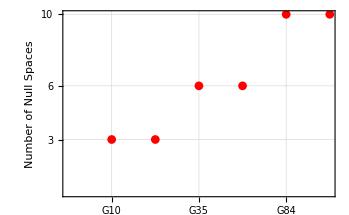

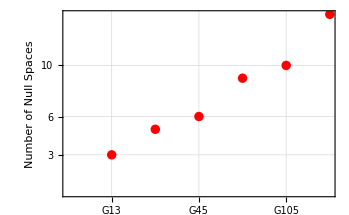

```mathematica
(*number of null spaces ordered as per the number of tensors*)
PlotDataFull=Table[{ii,NumNullSpacesFull⟦ii⟧},{ii,1,Length[NamesFullTheories]}];
PlotDataOrdered=Table[{ii,NumNullSpacesOrdered⟦ii⟧},{ii,1,Length[NamesOrderedTheories]}];

TicksFullTheories =Table[{ii,NamesFullTheories⟦ii⟧},{ii,1,Length[NamesFullTheories]}];

TicksOrderedTheories = Table[{ii,NamesOrderedTheories⟦ii⟧},{ii,1,Length[NamesOrderedTheories]}];

ListPlot[PlotDataFull,Frame->True,FrameTicks->{{NumNullSpacesFull,None},{TicksFullTheories,None}},GridLines->Automatic,FrameLabel->{{Style["Number of Null Spaces",FontSize->12,Black],None},{None,None}},FrameTicksStyle->Directive[FontSize->14,Black],PlotMarkers->Automatic,PlotStyle->{Thick,Red}]

ListPlot[PlotDataOrdered,Frame->True,FrameTicks->{{NumNullSpacesOrdered,None},{TicksOrderedTheories,None}},GridLines->Automatic,FrameLabel->{{Style["Number of Null Spaces",FontSize->12,Black],None},{None,None}},FrameTicksStyle->{{Directive[FontSize->14,Black],None},{Directive[FontSize->14,{Orange,Black}],None}},PlotStyle->{Thick,Red}]
```

```mathematica
TicksFullTheories
```

```mathematica
{{1,G10},{2,G20},{3,G35},{4,G56},{5,G84},{6,G120}}
```

# Rough Wok

```mathematica
(dx Ax26.var26 + dy Ay26.var26)/.MappingToConventional[8]//MatrixForm
```

(dx vx+dy vy
dx (θ+ρ+σxx)+dy σxy
dx σxy+dy (θ+ρ+σyy)
dx (-√(2/3) qx-√(2/3) vx)+dy (-√(2/3) qy-√(2/3) vy)
dx (mxxx/(√2)+(4 √2 qx)/15+(2 √2 vx)/3)+dy (mxxy/(√2)-(2 √2 qy)/15-(√2 vy)/3)
dy (mxyy/(√2)+(√2 qx)/5+vx/(√2))+dx (mxxy/(√2)+(√2 qy)/5+vy/(√2))
dx (mxyy/(√2)-(2 √2 qx)/15-(√2 vx)/3)+dy (myyy/(√2)+(4 √2 qy)/15+(2 √2 vy)/3)
dx (-Rxx/(√10)-Δ/(3 √10)-√(5/2) θ-√(2/5) σxx)+dy (-Rxy/(√10)-√(2/5) σxy)
dx (-Rxy/(√10)-√(2/5) σxy)+dy (-Ryy/(√10)-Δ/(3 √10)-√(5/2) θ-√(2/5) σyy)
dx (3/35 √(3/2) Rxx+3/5 √(3/2) σxx)+dy (-(√6 Rxy)/35-(√6 σxy)/5)
dx (4/35 √(2/3) Rxy+4/5 √(2/3) σxy)+dy (Rxx/(7 √6)-1/35 √(2/3) Ryy+σxx/(√6)-1/5 √(2/3) σyy)
dy (4/35 √(2/3) Rxy+4/5 √(2/3) σxy)+dx (-1/35 √(2/3) Rxx+Ryy/(7 √6)-1/5 √(2/3) σxx+σyy/(√6))
dx (-(√6 Rxy)/35-(√6 σxy)/5)+dy (3/35 √(3/2) Ryy+3/5 √(3/2) σyy)
2 √(2/15) dx qx+2 √(2/15) dy qy
dx (-mxxx/(√7)-(4 √7 qx)/15)+dy (-mxxy/(√7)+(2 √7 qy)/15)
dy (-mxyy/(√7)-(√7 qx)/5)+dx (-mxxy/(√7)-(√7 qy)/5)
dx (-mxyy/(√7)+(2 √7 qx)/15)+dy (-myyy/(√7)-(4 √7 qy)/15))

```mathematica
BC26//MatrixForm
```

(vx
mxxy/4+qy/10+vy/2+1/2 √(π/2) σxy
-√(π/10) qx-(√5 Rxx)/28-Δ/(15 √5)-(2 θ)/(√5)+(2 θW)/(√5)-σxx/(2 √5)
1/2 mxxx √(π/6)-Rxx/(140 √3)+(√3 Rxx)/70-Δ/(150 √3)+θ/(10 √3)-(√3 θ)/10-θW/(10 √3)+(√3 θW)/10+σxx/(10 √3)+(√3 σxx)/5
1/2 mxyy √(π/6)+Ryy/(28 √3)+Δ/(300 √3)-θ/(20 √3)+(√3 θ)/20+θW/(20 √3)-(√3 θW)/20-σxx/(10 √3)+σyy/(2 √3)
-mxxy/(4 √14)-(11 qy)/(10 √14)-1/4 √(π/7) Rxy+vy/(2 √14))

```mathematica
N[-√(2/3)1.275341]
```

-1.04131

```mathematica
?Floor
```

Floor[x] gives the greatest integer less than or equal to x. 
Floor[x,a] gives the greatest multiple of a less than or equal to x.

```mathematica
Floor[3.5]
```

3